```mathematica
Fsh[Q_,R_]:=4/3*Pi*R^3*3*(Sin[(Q*R)]-(Q*R)*Cos[(Q*R)])/(Q*R)^3
```

```mathematica
Vsh[R_]:=4/3*Pi*R^3
```

```mathematica
Limit[(Fsh[Q,R+x]-Fsh[Q,R])/(Vsh[R+x]-Vsh[R]),x->0]
```

Sin[Q R]/(Q R)

```mathematica
Vcyl[R_,L_]:=Pi*R^2*L
```

```mathematica
Fcyl[Q_,R_,L_]:=Vcyl[R,L]*Integrate[2*BesselJ[,1Q*R*Sin[x]]/(Q*R*Sin[x])*Sin[Q*L*Cos[x]]/(Q*L*Cos[x]),{x,0,Pi/2}]
```

```mathematica
FullSimplify[Fcyl[Q,R,L]]
```

L π R^2 ∫_0^(π/2) (2 BesselJ1[Q R Sin[x]] Csc[x] Sec[x] Sin[L Q Cos[x]])/(L Q^2 R)ⅆx

```mathematica
FunctionExpand[Integrate[2*BesselJ[1,Q*R*Sin[x]]/(Q*R), {x,0,Pi/2}, Assumptions->R>0 && Q>0]]
```

Integrate[(2 BesselJ[1,Q R Sin[x]])/(Q R),{x,0,π/2},Assumptions→R>0&&Q>0]

```mathematica
FunctionExpand[Integrate[(2*BesselJ[1,Q*R*Sin[x]]/(Q*R*Sin[x]))^2*Sin[x],{x,0,Pi/2}, Assumptions->R>=0 && Q>=0]]
```

2/(Q^2 R^2)-(2 BesselJ[1,2 Q R])/(Q^3 R^3)

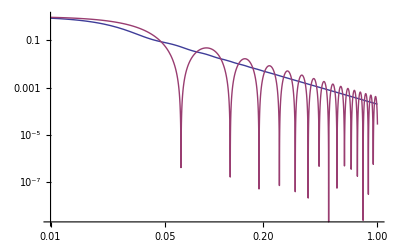

```mathematica
LogLogPlot[{(2/(Q^2 100^2)-(2 BesselJ[1,2 Q 100])/(Q^3 100^3))^(1),NIntegrate[(2*BesselJ[1,Q*100*Sin[x]]/(Q*100*Sin[x]))^1*Sin[x], {x,0,Pi/2}]^(1)},{Q,0.01,1}]
```